# Separate Ones by Zeros

"THE CHALLENGE"

Write a function to find the n^th term in a sequence of ones and zeros with a particular pattern.

## More Details

Consider the sequence 1, 0, 1, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, …, where the 1s are separated by one 0, two 0s, three 0s and so on.

## What Your Function Should Do

Write a function OneZero that takes as input a positive integer n and returns the nth term in the sequence.

```mathematica
OneZero[15]
```

1

### More Examples

```mathematica
OneZero[14]
```

0

```mathematica
OneZero[152076]
```

1

```mathematica
OneZero/@Range[28]
```

{1,0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1}

"SCRATCH AREA"

```mathematica
OneZero[152076]
```

1

```mathematica
OneZero[6]
```

1

```mathematica
Clear[OneZero]
```

```mathematica
OneZero/@Range[28]
```

{0,1,0,-1,1,0,-1,2,1,0,-1,-2,2,1,0,-1,-2,3,2,1,0,-1,-2,-3,3,2,1,0}

```mathematica
OneZero[n_Integer?Positive]:=
Module[{i,k},i=k=1;While[i<n,k++;i=i+k;];If[i==n,i=1,i=0];
i
]
```

```mathematica
OneZero[1]
```

1

```mathematica
Range[7.2]
```

{1,2,3,4,5,6,7}

```mathematica
Range@(Sqrt[2*5])
```

{1,2,3}

```mathematica
OneZero[n_Integer?Positive]:=Boole[Total@Range@Sqrt[2n]==n]
```

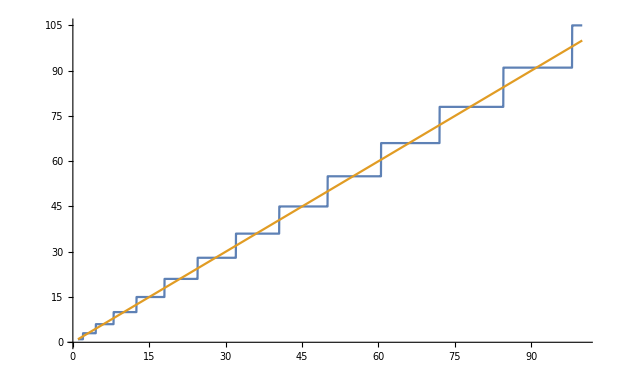

```mathematica
Plot[{Total@Range@Sqrt[2x],x},{x,1,100}]
```

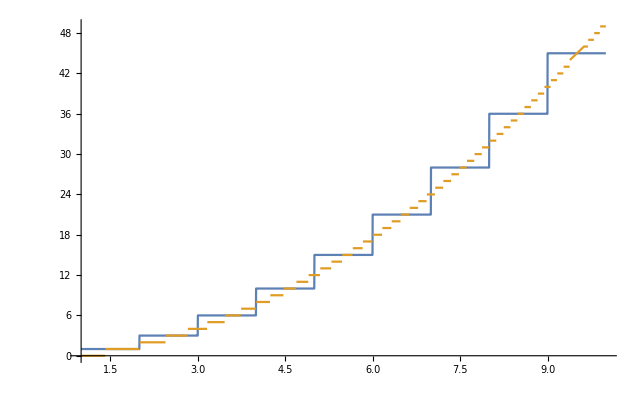

```mathematica
Plot[{Total@Range@x,Floor[x^2/2]},{x,1,10}]
```

"ENTER YOUR CODE HERE"

```mathematica
OneZero[n_Integer?Positive]:=Total@Range@Sqrt[2n]-n
```